Variational Quantum Classifier: Parity

Setuppaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierParity#2070070916 | Quantum Circuit Layerpaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierParity#1732304737
Datapaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierParity#1599589615 | Optimizationpaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierParity#1787628089

This demonstration is a translation of the tutorial “Variational classifierhttps://pennylane.ai/qml/demos/tutorial_variational_classifier” in PennyLane by Maria Schuld. It demonstrates variational quantum classifiers; that is, quantum circuits that can be trained from labelled data to classify new data samples.

In particular, we will see that the variational quantum classifier can reproduce the parity function f:{0,1}^n→{1,-1}, where f(x)=1 if there are even number of ones in x and -1 otherwise. This optimization example demonstrates how to encode binary inputs into the initial state of the variational circuit, which is simply a computational basis state.

BasisEmbeddingpaclet:QuantumMob/Q3/ref/BasisEmbeddingQuantumMob Package Symbol | Encodes data into amplitudes of a quantum state
FindMinimumpaclet:ref/FindMinimum | Find the minimum of a function

Frequently used function in variational classification.

Make sure to load the Q3 package.

```mathematica
Needs["QuantumMob`Q3`"]
```

Setup

The qubits to be modeled are S[i,$] for i=1,…,n.

```mathematica
Let[Qubit,S]
```

```mathematica
$n=4;
$N=Power[2,$n];
kk=Range[$n];
SS=S[kk,$]
```

{S_(,,1),S_(,,2),S_(,,3),S_(,,4)}

Data

Load and preprocess the data.

```mathematica
bits=Tuples[{0,1},$n];
parity=2*Mod[Count[#,1]&/@bits,2]-1;
data=AssociationThread[bits->parity];
Normal[data]//TableForm
```

{0,0,0,0}→-1
{0,0,0,1}→1
{0,0,1,0}→1
{0,0,1,1}→-1
{0,1,0,0}→1
{0,1,0,1}→-1
{0,1,1,0}→-1
{0,1,1,1}→1
{1,0,0,0}→1
{1,0,0,1}→-1
{1,0,1,0}→-1
{1,0,1,1}→1
{1,1,0,0}→-1
{1,1,0,1}→1
{1,1,1,0}→1
{1,1,1,1}→-1

Embed the input data to quantum states.

```mathematica
$in=BasisEmbedding[SS]/@Keys[data];
$in=Matrix/@$in;
MatrixForm/@$in
```

{(1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
1
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
1
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
1
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
1
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
1
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
1
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
1
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
1
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
1
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
1
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
1
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
1
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
1
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
1)}

Quantum Circuit Layer

The parameters to be optimized are a[layer,i,j] for i=1,…,n and j=1,…,3.

```mathematica
Let[Real,a]
```

Define a quantum circuit layer.

```mathematica
layer[aa_?MatrixQ,ss:{__?QubitQ}]:=QuantumCircuit[
Table[EulerRotation[aa[[k]],ss[[k]]],{k,kk}],
Apply[Sequence,CNOT@@@Transpose@{ss,RotateLeft@ss}]
]/;Length[aa]==Length[ss]
layer[aa_?MatrixQ]:=layer[aa,SS]
layer[n_Integer]:=QuantumCircuit@@Table[layer[Array[a[k],{$n,3}]],{k,n}]
```

For example, the following quantum circuit contains 24 real parameters, with three parameters a[k,i,1],a[k,i,2],a[k,i,3] associated with each qubit i on layer k.

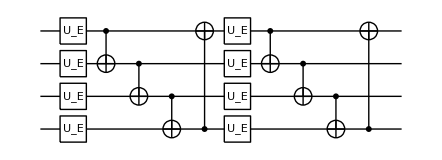

```mathematica
ll=layer[2]
```

Optimization

### Using a single layer

```mathematica
$L=1;
```

Pick a quantum circuit layer to apply on the input states.

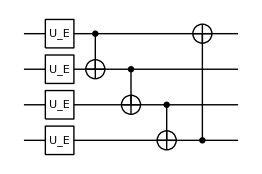

```mathematica
op=layer[$L]
```

```mathematica
mat=Normal@Matrix[op];
```

```mathematica
Z1=Matrix[S[1,3],SS];
```

```mathematica
w0=Flatten@RandomReal[{0,1}Pi,{$L,$n,3}]
```

{1.41694,0.769011,1.86193,2.64199,2.90684,1.28007,2.76019,2.58545,2.36391,1.93902,3.01061,1.32815}

The parameters to use.

```mathematica
aa=a[Range@$L,Range@$n,{1,2,3}];
```

The parameters are angles and the following constraints are imposed.

```mathematica
constraints=Thread[0<=aa<Pi];
```

```mathematica
optimizer[ww_]:=Module[
{ii=RandomChoice[Range@Length@data,4],
yy,vv,avg,sol,cost},
yy=Part[Values@data,ii];
vv=Transpose@Part[$in,ii];
vv=Transpose[mat.vv];
avg=Map[Conjugate[#].Z1.#&,vv];
cost=Mean@Abs[avg-yy]^2;
EchoTiming[
{cost,sol}=FindMinimum[{cost,constraints},Transpose@{aa,ww},
StepMonitor:>PrintTemporary["Cost: ",cost],
Method->"IPOPT"];
];
Echo[{Chop[avg/.sol],yy,cost},"{avg, yy, cost}"];
Return[aa/.sol]
]
```

Test the optimizer.

```mathematica
optimizer[w0]
```

0.217922

{avg, yy, cost}  {{0.999999,-0.999999,0.999999,-0.999999},{1,-1,-1,-1},0.250001}

{1.57077,1.57082,1.57097,1.57071,3.14082,1.5707,1.57087,0.000948503,1.57059,1.57072,3.14086,1.5707}

Find the optimal values of the parameters iteratively.

```mathematica
$R=5;(* the number of iterations *)
ww=Nest[optimizer,w0,$R]
```

0.098922

{avg, yy, cost}  {{0.999998,-0.999998,0.999998,0.999998},{1,-1,1,-1},0.250001}

0.054929

{avg, yy, cost}  {{-0.851835,0.851835,0.851835,0.851835},{-1,1,-1,-1},1.}

0.207805

{avg, yy, cost}  {{1.,-1.,1.,-1.},{1,1,1,-1},0.25}

0.081851

{avg, yy, cost}  {{-0.999999,0.999999,-0.999999,-0.999999},{-1,1,-1,1},0.250001}

0.094613

{avg, yy, cost}  {{0.999714,0.999714,0.999714,-0.999714},{1,1,1,-1},8.1801×10^-8}

{1.5708,1.57079,1.5708,1.5708,3.12778,1.5708,1.5708,0.0137976,1.5708,1.5708,3.12778,1.57079}

From the optimized parameters, make predictions.

```mathematica
mm=mat/.Thread[aa->ww];
vv=Transpose[mm.Transpose[$in]];
predicted=Map[Sign@Chop[Conjugate[#].Z1.#]&,vv]
```

{1,-1,-1,1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1}

```mathematica
predicted-Values[data]
```

{2,-2,-2,2,-2,2,2,-2,0,0,0,0,0,0,0,0}

#### Verdict

A single-layer is not sufficient to predict the parity values properly.

Using the Method->“IPOPT”, FindMinimum is significantly faster than the default method or any other documented methods (IPOTP seems to refer to the non-linear interior-point method from the IPOPT library).

### Using two layers without imposing the constraints

```mathematica
$L=2;
```

Pick a quantum circuit layer to apply on the input states.

```mathematica
op=layer[$L]
```

-Graphics-

Check which parameters are actually involved in the above quantum circuit.

```mathematica
param=Cases[op,_a,Infinity]
Length[param]
```

{a_(,,111),a_(,,112),a_(,,113),a_(,,121),a_(,,122),a_(,,123),a_(,,131),a_(,,132),a_(,,133),a_(,,141),a_(,,142),a_(,,143),a_(,,211),a_(,,212),a_(,,213),a_(,,221),a_(,,222),a_(,,223),a_(,,231),a_(,,232),a_(,,233),a_(,,241),a_(,,242),a_(,,243)}

24

```mathematica
mat=Normal@N@Matrix[op];
Dimensions[mat]
```

{16,16}

```mathematica
Z1=Matrix[S[1,3],SS];
Dimensions[Z1]
```

{16,16}

```mathematica
w0=Flatten@RandomReal[{0,1}Pi,{$L,$n,3}]
Length[w0]
```

{1.93329,2.26278,0.686629,1.62111,2.5782,2.91305,2.6135,1.87458,1.17216,1.56133,1.05992,2.55119,1.29986,1.17718,2.31488,2.57335,3.05784,0.0302265,1.46013,2.05696,1.39595,0.463257,0.507191,1.09723}

24

The set of parameters.

```mathematica
aa=a[Range@$L,Range@$n,{1,2,3}];
```

We prepare the natural constraints, but in this example, we will not impose them.

```mathematica
constraints=Thread[0<=aa<Pi];
```

```mathematica
Clear[optimizer];
optimizer[ww_]:=Module[
{ii=RandomChoice[Range@Length@data,4],
yy,vv,avg,sol,cost},
Echo[ii,"ii"];
yy=Part[Values@data,ii];
vv=Transpose@SparseArray@Part[$in,ii];
vv=Transpose[mat.vv];
avg=Map[Conjugate[#].Z1.#&,vv];
cost=Mean@Abs[avg-yy]^2;
Echo[{avg,cost}/.Thread[aa->ww]//Chop,"{avg, cost}"];
EchoTiming[
{cost,sol}=FindMinimum[{cost,constraints},Transpose@{aa,ww},
StepMonitor:>PrintTemporary["Cost: ",cost],
Method->"IPOPT"];
];
Echo[{Chop[avg/.sol],yy,cost},"{avg, yy, cost}"];
Return[aa/.sol]
]
```

Test the optimizer.

```mathematica
optimizer[w0]
```

ii  {3,16,15,3}

{avg, cost}  {{-0.254145,0.255505,-0.242823,-0.254145},1.56664}

1.50845

{avg, yy, cost}  {{0.999748,-0.99978,0.999716,0.999748},{1,-1,1,1},6.34222×10^-8}

{1.8722,1.91053,0.992666,1.59109,2.11819,2.33817,1.57123,1.57359,1.29222,1.5708,1.57364,2.19823,1.37992,1.29561,2.07005,2.20895,3.12941,0.695914,1.49238,1.55623,0.0118494,0.885384,0.0193208,1.28827}

Find the optimal values of the parameters iteratively.

```mathematica
$R=3;(* the number of iterations *)
ww=Nest[optimizer,w0,$R]
```

ii  {14,6,13,1}

{avg, cost}  {{-0.341873,0.457961,0.32587,0.329463},1.85993}

1.56257

{avg, yy, cost}  {{0.999834,-0.999834,-0.999834,-0.999832},{1,-1,-1,-1},2.772×10^-8}

ii  {3,15,9,5}

{avg, cost}  {{-0.0000480283,-0.0000480304,0.999832,0.999834},0.250107}

1.26423

{avg, yy, cost}  {{0.999738,0.999738,0.999738,0.999738},{1,1,1,1},6.85859×10^-8}

ii  {5,2,10,16}

{avg, cost}  {{0.999738,0.999738,-0.999738,-0.999737},6.86221×10^-8}

1.12608

{avg, yy, cost}  {{0.999841,0.999841,-0.999841,-0.999335},{1,1,-1,-1},8.161×10^-8}

{1.5708,1.5708,1.5708,1.5708,1.57873,1.5708,3.12778,1.5708,1.5708,1.5708,3.12566,1.57079,1.5708,1.5708,1.5708,1.5708,3.12566,1.57084,1.5708,1.57873,1.5708,1.5708,1.5708,1.5708}

From the optimized parameters, make predictions.

```mathematica
mm=mat/.Thread[aa->ww];
vv=Transpose[mm.Transpose[$in]];
predicted=Map[Sign@Chop[Conjugate[#].Z1.#]&,vv]
```

{-1,1,1,-1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1}

```mathematica
predicted-Values[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Verdict

Two layers is sufficient to properly predict the parity values.

Using the Method->“IPOPT”, FindMinimum is significantly faster than the default method or any other documented methods (IPOTP seems to refer to the non-linear interior-point method from the IPOPT library).

Otherwise, FindMinimum is rather slow to handle 24 parameters.

### Using two layers imposing the constraints

```mathematica
$L=2;
```

Pick a quantum circuit layer to apply on the input states.

```mathematica
op=layer[$L]
```

-Graphics-

Check which parameters are actually involved in the above quantum circuit.

```mathematica
param=Cases[op,_a,Infinity]
Length[param]
```

{a_(,,111),a_(,,112),a_(,,113),a_(,,121),a_(,,122),a_(,,123),a_(,,131),a_(,,132),a_(,,133),a_(,,141),a_(,,142),a_(,,143),a_(,,211),a_(,,212),a_(,,213),a_(,,221),a_(,,222),a_(,,223),a_(,,231),a_(,,232),a_(,,233),a_(,,241),a_(,,242),a_(,,243)}

24

```mathematica
mat=Normal@N@Matrix[op];
Dimensions[mat]
```

{16,16}

```mathematica
Z1=Matrix[S[1,3],SS];
Dimensions[Z1]
```

{16,16}

```mathematica
w0=Flatten@RandomReal[{0,1}Pi,{$L,$n,3}]
Length[w0]
```

{1.94557,0.987589,1.52208,2.94959,2.35561,1.66824,2.2028,0.524378,0.803101,0.62935,1.42017,1.3263,1.92535,0.314953,1.3737,2.54746,3.0801,3.05675,2.81035,0.551871,1.34187,2.81354,2.20244,0.637963}

24

The set of parameters.

```mathematica
aa=a[Range@$L,Range@$n,{1,2,3}];
```

Prepare the natural constraints for angles.

```mathematica
constraints=Thread[0<=aa<Pi];
```

```mathematica
Clear[optimizer];
optimizer[ww_]:=Module[
{ii=RandomChoice[Range@Length@data,4],
yy,vv,avg,sol,cost},
Echo[ii,"ii"];
yy=Part[Values@data,ii];
vv=Transpose@SparseArray@Part[$in,ii];
vv=Transpose[mat.vv];
avg=Map[Conjugate[#].Z1.#&,vv];
cost=Mean@Abs[avg-yy]^2;
Echo[{avg,cost}/.Thread[aa->ww]//Chop,"{avg, cost}"];
EchoTiming[
{cost,sol}=FindMinimum[{cost,constraints},Transpose@{aa,ww},
StepMonitor:>PrintTemporary["Cost: ",cost],
Method->"IPOPT"]
];
Echo[{Chop[avg/.sol],yy,cost},"{avg, yy, cost}"];
Return[aa/.sol]
]
```

Test the optimizer.

```mathematica
optimizer[w0]
```

ii  {3,10,3,5}

{avg, cost}  {{-0.147205,0.038868,-0.147205,-0.117774},1.23824}

1.42203

{avg, yy, cost}  {{0.999685,-0.99955,0.999685,0.999456},{1,-1,1,1},1.64788×10^-7}

{0.0106772,1.5708,1.55935,3.13092,1.5708,1.59376,1.61172,0.0227123,1.35159,0.0106781,1.5708,1.51202,1.6581,1.13505,1.52381,1.87568,3.1226,1.76937,1.99868,0.0183635,1.1227,2.00022,1.5708,0.0106768}

Find the optimal values of the parameters iteratively.

```mathematica
$R=3;(* the number of iterations *)
ww=Nest[optimizer,w0,$R]
```

ii  {3,7,6,10}

{avg, cost}  {{-0.147205,0.110461,0.0432805,0.038868},1.17712}

1.49349

{avg, yy, cost}  {{0.999661,-0.999661,-0.999661,-0.999661},{1,-1,-1,-1},1.14671×10^-7}

ii  {3,10,15,14}

{avg, cost}  {{0.999661,-0.999661,0.999661,0.999661},1.14671×10^-7}

1.18906

{avg, yy, cost}  {{0.999686,-0.999686,0.999686,0.999686},{1,-1,1,1},9.84594×10^-8}

ii  {1,12,2,7}

{avg, cost}  {{-0.998849,0.998849,0.999686,-0.999686},5.36633×10^-7}

1.16684

{avg, yy, cost}  {{-0.999669,0.999669,0.999724,-0.999571},{-1,1,1,-1},1.167×10^-7}

{1.55968,1.5708,1.57081,1.57075,3.12961,1.57077,1.5708,1.5708,1.57078,0.011966,1.5708,1.57074,1.57076,1.5707,1.57079,1.57078,1.5708,3.12692,1.57089,0.012813,2.22239,1.57078,1.5708,0.0119663}

From the optimized parameters, make predictions.

```mathematica
mm=mat/.Thread[aa->ww];
vv=Transpose[mm.Transpose[$in]];
predicted=Map[Sign@Chop[Conjugate[#].Z1.#]&,vv]
```

{-1,1,1,-1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1}

```mathematica
predicted-Values[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Verdict

Two layers is sufficient to properly predict the parity values.

Using the Method->“IPOPT”, FindMinimum is significantly faster than the default method or any other documented methods (IPOTP seems to refer to the non-linear interior-point method from the IPOPT library).

Otherwise, FindMinimum is rather slow to handle 24 parameters.

| Related Guides
▪Quantum Information Systems
▪Quantum Many-Body Systems
▪Quantum Spin Systems

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Information Systems with Q3
▪Quantum Many-Body Systems with Q3
▪Quantum Spin Systems with Q3

| Related Links
Maria Should, PennyLane demonstration “Variational classifierhttps://pennylane.ai/qml/demos/tutorial_variational_classifier”.
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).